# 28: Basic QR Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

The book says “Compute the QR decomposition, flip the order of the factors and repeat!”. Here is an example for a symmetric matrix. It does become

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergReduction[A]];
TabView[
Table[
{Q,R}=QRDecomposition[T];Q=Qᵀ;
T=Chop[R.Q];
MatrixPlot[T],
{MaxIter}]
]
```

12345678910111213141516171819202122

```mathematica
TabView[{
"T_0"->MatrixForm[T0],
"T_-1"->MatrixForm[T]}]
```

12

It is pretty clear that something is driving the off-diagonals to zero. We want to understand what is doing this. Once we understand that we might be able to make it go faster!

## ¢

```mathematica
HessenbergReduction[AIn_]:= Module[{A=AIn, m=Length[A],x},
Do[
x=A⟦k+1;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧+Sign[x⟦1⟧]*Norm[x];
v=Normalize[v];
A⟦k+1;;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦k+1;;m,k;;m⟧];
A⟦1;;m,k+1;;m⟧=A⟦1;;m,k+1;;m⟧-2 KroneckerProduct[A⟦1;;m,k+1;;m⟧.v,v],
{k,1,m-2}];
Chop[A]]
```

## Back to the earlier bad idea.

Householder reflections are good for introducing zeros in bulk. Remember Givens rotations
	(p1 | -p2
p2 | p1)
and 
	(p1 | -p2 | -p3 | -p4
p2 | p1 | -p4 | p3
p3 | p4 | p1 | -p2
p4 | -p3 | p2 | p1)
and
	(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | p4 | -p3 | p6 | -p5 | -p8 | p7
-p3 | -p4 | p1 | p2 | p7 | p8 | -p5 | -p6
-p4 | p3 | -p2 | p1 | p8 | -p7 | p6 | -p5
-p5 | -p6 | -p7 | -p8 | p1 | p2 | p3 | p4
-p6 | p5 | -p8 | p7 | -p2 | p1 | -p4 | p3
-p7 | p8 | p5 | -p6 | -p3 | p4 | p1 | -p2
-p8 | -p7 | p6 | p5 | -p4 | -p3 | p2 | p1)
are orthogonal for unit vectors.

#### Traditional G_2 for Real Tridiagonal Matrix T

The top corner of a symmetric tridiagonal matrix T looks like
	T=(d_1 | u_1 | 0 | ⋯
u_1 | d_2 | u_2 |  
0 | u_2 | d_3 | ⋱
⋮ |   | ⋱ | ⋱)
The Givens rotation
	Q=(G_2 | 0
0 | I_(m-2))=((p_1 | -p_2
p_2 | p_1) | 0
0 | I_(m-2))
zeros the top subdiagonal entry in the product
	Q.T=(d_1 p_1-p_2 u_1 | -d_2 p_2+p_1 u_1 | -p_2 u_2 | 0 | 0
d_1 p_2+p_1 u_1 | d_2 p_1+p_2 u_1 | p_1 u_2 | 0 | 0
0 | u_2 | d_3 | u_3 | 0
0 | 0 | u_3 | d_4 | u_4
0 | 0 | 0 | u_4 | d_5)
if {p_1,p_2} is a unit vector perpendicular to {d_1,u_1}.  Of course, to preserve eigenvalues we need the similarity transformation
	Q.T.Qᵀ=(d_1 p_1^2+p_2 (d_2 p_2-2 p_1 u_1) | d_1 p_1 p_2-d_2 p_1 p_2+(p_1^2-p_2^2) u_1 | -p_2 u_2 | 0 | 0
d_1 p_1 p_2-d_2 p_1 p_2+(p_1^2-p_2^2) u_1 | d_2 p_1^2+p_2 (d_1 p_2+2 p_1 u_1) | p_1 u_2 | 0 | 0
-p_2 u_2 | p_1 u_2 | d_3 | u_3 | 0
0 | 0 | u_3 | d_4 | u_4
0 | 0 | 0 | u_4 | d_5)
which destroys one of the zeros we worked hard to create. O

```mathematica
Clear[Subscript]
m=7;
dd=Table[Subscript[d, i],{i,m}];uu=Table[Subscript[u, i],{i,m-1}];
T=SparseArray[{Band[{1,1}]->dd,Band[{1,2}]->uu,Band[{2,1}]->uu},{m,m}];
Q=IdentityMatrix[m];Q⟦1;;2,1;;2⟧={{Subscript[p, 1],-Subscript[p, 2]},{Subscript[p, 2],Subscript[p, 1]}};
Simplify[MatrixForm[Q.T]]
Simplify[MatrixForm[Q.T]/.{Subscript[p, 1]->(-Subscript[d, 1])/(√(Subscript[d, 1]^2+Subscript[u, 1]^2)),Subscript[p, 2]-> Subscript[u, 1]/(√(Subscript[d, 1]^2+Subscript[u, 1]^2))}]
Simplify[MatrixForm[Q.T.Qᵀ]]
Simplify[MatrixForm[Q.T.Qᵀ]/.{Subscript[p, 1]->(-Subscript[d, 1])/(√(Subscript[d, 1]^2+Subscript[u, 1]^2)),Subscript[p, 2]-> Subscript[u, 1]/(√(Subscript[d, 1]^2+Subscript[u, 1]^2))}]
```

(d_1 p_1-p_2 u_1 | -d_2 p_2+p_1 u_1 | -p_2 u_2 | 0 | 0 | 0 | 0
d_1 p_2+p_1 u_1 | d_2 p_1+p_2 u_1 | p_1 u_2 | 0 | 0 | 0 | 0
0 | u_2 | d_3 | u_3 | 0 | 0 | 0
0 | 0 | u_3 | d_4 | u_4 | 0 | 0
0 | 0 | 0 | u_4 | d_5 | u_5 | 0
0 | 0 | 0 | 0 | u_5 | d_6 | u_6
0 | 0 | 0 | 0 | 0 | u_6 | d_7)

(-√(d_1^2+u_1^2) | -((d_1+d_2) u_1)/(√(d_1^2+u_1^2)) | -(u_1 u_2)/(√(d_1^2+u_1^2)) | 0 | 0 | 0 | 0
0 | (-d_1 d_2+u_1^2)/(√(d_1^2+u_1^2)) | -(d_1 u_2)/(√(d_1^2+u_1^2)) | 0 | 0 | 0 | 0
0 | u_2 | d_3 | u_3 | 0 | 0 | 0
0 | 0 | u_3 | d_4 | u_4 | 0 | 0
0 | 0 | 0 | u_4 | d_5 | u_5 | 0
0 | 0 | 0 | 0 | u_5 | d_6 | u_6
0 | 0 | 0 | 0 | 0 | u_6 | d_7)

(d_1 p_1^2+p_2 (d_2 p_2-2 p_1 u_1) | d_1 p_1 p_2-d_2 p_1 p_2+(p_1^2-p_2^2) u_1 | -p_2 u_2 | 0 | 0 | 0 | 0
d_1 p_1 p_2-d_2 p_1 p_2+(p_1^2-p_2^2) u_1 | d_2 p_1^2+p_2 (d_1 p_2+2 p_1 u_1) | p_1 u_2 | 0 | 0 | 0 | 0
-p_2 u_2 | p_1 u_2 | d_3 | u_3 | 0 | 0 | 0
0 | 0 | u_3 | d_4 | u_4 | 0 | 0
0 | 0 | 0 | u_4 | d_5 | u_5 | 0
0 | 0 | 0 | 0 | u_5 | d_6 | u_6
0 | 0 | 0 | 0 | 0 | u_6 | d_7)

((d_1^3+2 d_1 u_1^2+d_2 u_1^2)/(d_1^2+u_1^2) | (d_1 d_2 u_1-u_1^3)/(d_1^2+u_1^2) | -(u_1 u_2)/(√(d_1^2+u_1^2)) | 0 | 0 | 0 | 0
(d_1 d_2 u_1-u_1^3)/(d_1^2+u_1^2) | (d_1 (d_1 d_2-u_1^2))/(d_1^2+u_1^2) | -(d_1 u_2)/(√(d_1^2+u_1^2)) | 0 | 0 | 0 | 0
-(u_1 u_2)/(√(d_1^2+u_1^2)) | -(d_1 u_2)/(√(d_1^2+u_1^2)) | d_3 | u_3 | 0 | 0 | 0
0 | 0 | u_3 | d_4 | u_4 | 0 | 0
0 | 0 | 0 | u_4 | d_5 | u_5 | 0
0 | 0 | 0 | 0 | u_5 | d_6 | u_6
0 | 0 | 0 | 0 | 0 | u_6 | d_7)

```mathematica
Subscript[d, 1] Subscript[p, 1] Subscript[p, 2]-Subscript[d, 2] Subscript[p, 1] Subscript[p, 2]+(Subscript[p, 1]^2-Subscript[p, 2]^2) Subscript[u, 1]
```

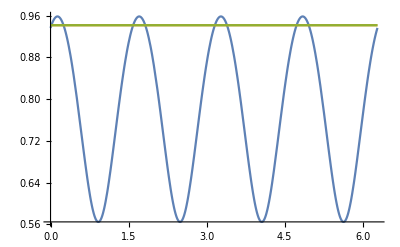

```mathematica
Clear[Subscript,f,θ]
{Subscript[d, 1],Subscript[d, 2],Subscript[u, 1],Subscript[u, 2]}=RandomReal[{-1,1},4];
f[θ_]:=Module[{p1=Cos[θ],p2=Sin[θ]},
Norm[{Subscript[d, 1] p1 p2-Subscript[d, 2] p1 p2+(p1^2-p2^2) Subscript[u, 1],p2 Subscript[u, 2],p1 Subscript[u, 2]}]
];
RoughValue1 = Norm[{Subscript[d, 1] p1 p2-Subscript[d, 2] p1 p2+(p1^2-p2^2) Subscript[u, 1],p2 Subscript[u, 2],p1 Subscript[u, 2]}]/.{p1->(-Subscript[d, 1])/(√(Subscript[d, 1]^2+Subscript[u, 1]^2)),p2-> Subscript[u, 1]/(√(Subscript[d, 1]^2+Subscript[u, 1]^2))};
RoughValue2 = Norm[{Subscript[d, 1] p1 p2-Subscript[d, 2] p1 p2+(p1^2-p2^2) Subscript[u, 1],p2 Subscript[u, 2],p1 Subscript[u, 2]}]/.{p1->Subscript[d, 1]/(√(Subscript[d, 1]^2+Subscript[u, 1]^2)),p2-> (-Subscript[u, 1])/(√(Subscript[d, 1]^2+Subscript[u, 1]^2))};
Plot[{f[θ], RoughValue1,RoughValue2 },{θ,0, 2π},
PlotRange->All]
```

#### G_4 for Real Tridiagonal Matrix T

The top corner of a symmetric tridiagonal matrix T looks like
	T=(d_1 | u_1 | 0 | ⋯
u_1 | d_2 | u_2 |  
0 | u_2 | d_3 | ⋱
⋮ |   | ⋱ | ⋱)
The Givens rotation 
	Q=(G_4 | 0
0 | I_(m-4))=((p1 | -p2 | -p3 | -p4
p2 | p1 | -p4 | p3
p3 | p4 | p1 | -p2
p4 | -p3 | p2 | p1) | 0
0 | I_(m-4))
zeros the top subdiagonal entry in the product
	Q.T=(d_1 p_1-p_2 u_1 | -d_2 p_2+p_1 u_1 | -p_2 u_2 | 0 | 0
d_1 p_2+p_1 u_1 | d_2 p_1+p_2 u_1 | p_1 u_2 | 0 | 0
0 | u_2 | d_3 | u_3 | 0
0 | 0 | u_3 | d_4 | u_4
0 | 0 | 0 | u_4 | d_5)
if {p_1,p_2} is a unit vector perpendicular to {d_1,u_1}.  Of course, to preserve eigenvalues we need the similarity transformation
	Q.T.Qᵀ=(d_1 p_1^2+p_2 (d_2 p_2-2 p_1 u_1) | d_1 p_1 p_2-d_2 p_1 p_2+(p_1^2-p_2^2) u_1 | -p_2 u_2 | 0 | 0
d_1 p_1 p_2-d_2 p_1 p_2+(p_1^2-p_2^2) u_1 | d_2 p_1^2+p_2 (d_1 p_2+2 p_1 u_1) | p_1 u_2 | 0 | 0
-p_2 u_2 | p_1 u_2 | d_3 | u_3 | 0
0 | 0 | u_3 | d_4 | u_4
0 | 0 | 0 | u_4 | d_5)
which destroys one of the zeros we worked hard to create. O

```mathematica
Clear[Subscript]
m=7;
dd=Table[Subscript[d, i],{i,m}];uu=Table[Subscript[u, i],{i,m-1}];
T=Table[t[i,j],{i,m},{j,m}];
T=LowerTriangularize[T];
T=T+Transpose[LowerTriangularize[T,-1]];
MatrixForm[T];
Q=IdentityMatrix[m];Q⟦1;;4,1;;4⟧=({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}});
Simplify[MatrixForm[Q.T]];
Hmm=Q.T.Qᵀ;
{A0,A1}=CoefficientArrays[D[Hmm⟦1,1⟧,{{p1,p2,p3,p4}}],{p1,p2,p3,p4}];
MatrixForm[A1]
MatrixForm[Normal[A1]/.{t[i_,j_]:>tt[i,Abs[i-j]]}]
```

(2 t[1,1] | -2 t[2,1] | -2 t[3,1] | -2 t[4,1]
-2 t[2,1] | 2 t[2,2] | 2 t[3,2] | 2 t[4,2]
-2 t[3,1] | 2 t[3,2] | 2 t[3,3] | 2 t[4,3]
-2 t[4,1] | 2 t[4,2] | 2 t[4,3] | 2 t[4,4])

(2 tt[1,0] | -2 tt[2,1] | -2 tt[3,2] | -2 tt[4,3]
-2 tt[2,1] | 2 tt[2,0] | 2 tt[3,1] | 2 tt[4,2]
-2 tt[3,2] | 2 tt[3,1] | 2 tt[3,0] | 2 tt[4,1]
-2 tt[4,3] | 2 tt[4,2] | 2 tt[4,1] | 2 tt[4,0])

So A1 is symmetric.  It is not generically non-invertible. It is generically invertible with the third off diagonals zero t[4,1] and t[1,4].
The top diagonal entry is a pure symmetric quadratic!  I have a quadratic constraint ||p||=1. I want to approximate the extreme (most negative or most positive eigenvalue). In practice, this is pretty cheap.

```mathematica
Expand[Hmm⟦1,1⟧]
```

p1^2 t[1,1]-2 p1 p2 t[2,1]+p2^2 t[2,2]-2 p1 p3 t[3,1]+2 p2 p3 t[3,2]+p3^2 t[3,3]-2 p1 p4 t[4,1]+2 p2 p4 t[4,2]+2 p3 p4 t[4,3]+p4^2 t[4,4]

```mathematica
Solve[Det[A1]==0 ]
```

{{t[4,4]→(t[3,2]^2 t[4,1]^2-t[2,2] t[3,3] t[4,1]^2-2 t[3,1] t[3,2] t[4,1] t[4,2]+2 t[2,1] t[3,3] t[4,1] t[4,2]+t[3,1]^2 t[4,2]^2-t[1,1] t[3,3] t[4,2]^2+2 t[2,2] t[3,1] t[4,1] t[4,3]-2 t[2,1] t[3,2] t[4,1] t[4,3]-2 t[2,1] t[3,1] t[4,2] t[4,3]+2 t[1,1] t[3,2] t[4,2] t[4,3]+t[2,1]^2 t[4,3]^2-t[1,1] t[2,2] t[4,3]^2)/(t[2,2] t[3,1]^2-2 t[2,1] t[3,1] t[3,2]+t[1,1] t[3,2]^2+t[2,1]^2 t[3,3]-t[1,1] t[2,2] t[3,3])},{t[2,2]→(t[2,1] t[3,2] t[4,1]+t[2,1] t[3,1] t[4,2]-t[1,1] t[3,2] t[4,2]-t[2,1]^2 t[4,3])/(t[3,1] t[4,1]-t[1,1] t[4,3]),t[3,3]→(t[3,1] t[3,2] t[4,1]-t[3,1]^2 t[4,2]+t[2,1] t[3,1] t[4,3]-t[1,1] t[3,2] t[4,3])/(t[2,1] t[4,1]-t[1,1] t[4,2])},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[2,2]→(t[2,1] t[3,2])/t[3,1],t[3,3]→(t[3,1] t[3,2])/t[2,1]},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[2,2]→(t[2,1] t[3,2])/t[3,1],t[4,2]→(t[3,2] t[4,1])/t[3,1]},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[3,3]→(t[3,1] t[3,2])/t[2,1],t[4,3]→(t[3,2] t[4,1])/t[2,1]},{t[1,1]→(t[2,1] t[4,1])/t[4,2],t[3,3]→(-t[2,1] t[3,2]^2 t[4,1]-t[2,2] t[3,1]^2 t[4,2]+2 t[2,1] t[3,1] t[3,2] t[4,2])/(t[2,1] (-t[2,2] t[4,1]+t[2,1] t[4,2])),t[4,3]→(t[3,1] t[4,2])/t[2,1]},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[3,3]→t[3,2]^2/t[2,2]},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[4,1]→0},{t[1,1]→(t[3,1] t[4,1])/t[4,3],t[2,1]→0,t[3,2]→0,t[3,3]→(t[3,1] t[4,3])/t[4,1]},{t[2,1]→0,t[2,2]→0,t[3,2]→0,t[3,3]→t[3,1]^2/t[1,1]},{t[2,1]→0,t[2,2]→0,t[3,2]→0,t[4,2]→0},{t[1,1]→(t[3,1] t[4,1])/t[4,3],t[2,1]→0,t[3,3]→(t[3,2]^2 t[4,1]+t[2,2] t[3,1] t[4,3])/(t[2,2] t[4,1]),t[4,2]→0},{t[1,1]→0,t[2,1]→0,t[2,2]→0,t[4,2]→(t[3,2] t[4,1])/t[3,1]},{t[1,1]→(t[2,1] t[4,1])/t[4,2],t[2,2]→(t[2,1] t[4,2])/t[4,1],t[3,1]→0,t[3,2]→0},{t[2,2]→t[2,1]^2/t[1,1],t[3,1]→0,t[3,2]→0,t[3,3]→0},{t[3,1]→0,t[3,2]→0,t[3,3]→0,t[4,3]→0},{t[1,1]→(t[2,1] t[4,1])/t[4,2],t[3,1]→0,t[3,3]→(t[3,2]^2 t[4,1])/(t[2,2] t[4,1]-t[2,1] t[4,2]),t[4,3]→0},{t[3,3]→(-t[2,2] t[3,1]^2+2 t[2,1] t[3,1] t[3,2]-t[1,1] t[3,2]^2)/(t[2,1]^2-t[1,1] t[2,2]),t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[3,3]→(t[3,1] t[3,2])/t[2,1],t[4,1]→0,t[4,3]→0},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[2,2]→(t[2,1] t[3,2])/t[3,1],t[4,2]→(t[3,2] t[4,1])/t[3,1],t[4,3]→(t[3,2] t[4,1])/t[2,1]},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[2,2]→(t[2,1] t[3,2])/t[3,1],t[3,3]→(t[3,1] t[3,2])/t[2,1],t[4,3]→(t[3,2] t[4,1])/t[2,1]},{t[1,1]→0,t[2,1]→0,t[2,2]→0,t[3,1]→0,t[3,2]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[3,2]→0,t[4,1]→0},{t[2,1]→0,t[3,1]→0,t[3,2]→0,t[3,3]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[4,1]→0,t[4,3]→0},{t[2,1]→0,t[3,1]→0,t[3,3]→t[3,2]^2/t[2,2],t[4,2]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[3,3]→t[3,2]^2/t[2,2],t[4,3]→0},{t[1,1]→(t[3,1] t[4,1])/t[4,3],t[2,1]→0,t[2,2]→0,t[3,2]→0,t[3,3]→(t[3,1] t[4,3])/t[4,1]},{t[2,1]→0,t[3,2]→0,t[3,3]→t[3,1]^2/t[1,1],t[4,1]→0,t[4,3]→0},{t[1,1]→(t[3,1] t[4,1])/t[4,3],t[2,1]→0,t[2,2]→0,t[3,2]→0,t[4,2]→0},{t[1,1]→0,t[2,1]→0,t[2,2]→0,t[4,1]→0,t[4,2]→0},{t[2,1]→0,t[3,3]→(t[2,2] t[3,1]^2+t[1,1] t[3,2]^2)/(t[1,1] t[2,2]),t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[2,2]→t[2,1]^2/t[1,1],t[3,1]→0,t[3,2]→0,t[4,1]→0,t[4,2]→0},{t[1,1]→(t[2,1] t[4,1])/t[4,2],t[2,2]→(t[2,1] t[4,2])/t[4,1],t[3,1]→0,t[3,2]→0,t[4,3]→0},{t[2,2]→t[2,1]^2/t[1,1],t[3,1]→0,t[3,2]→0,t[3,3]→0,t[4,3]→0},{t[3,1]→0,t[3,3]→(t[1,1] t[3,2]^2)/(-t[2,1]^2+t[1,1] t[2,2]),t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[3,2]→0,t[3,3]→(t[2,2] t[3,1]^2)/(-t[2,1]^2+t[1,1] t[2,2]),t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[2,2]→(t[2,1] t[3,2])/t[3,1],t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[1,1]→(t[2,1] t[3,1])/t[3,2],t[2,2]→(t[2,1] t[3,2])/t[3,1],t[3,3]→(t[3,1] t[3,2])/t[2,1],t[4,1]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[3,2]→0,t[4,1]→0,t[4,3]→0},{t[2,1]→0,t[2,2]→0,t[3,1]→0,t[3,2]→0,t[4,2]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[2,2]→0,t[3,1]→0,t[3,2]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[3,2]→0,t[3,3]→0,t[4,3]→0},{t[2,1]→0,t[2,2]→0,t[3,1]→0,t[3,2]→0,t[3,3]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[3,1]→0,t[3,3]→t[3,2]^2/t[2,2],t[4,2]→0,t[4,3]→0},{t[2,1]→0,t[2,2]→0,t[3,2]→0,t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[2,1]→0,t[2,2]→0,t[3,2]→0,t[3,3]→t[3,1]^2/t[1,1],t[4,1]→0,t[4,3]→0},{t[1,1]→0,t[2,1]→0,t[2,2]→0,t[4,1]→0,t[4,2]→0,t[4,3]→0},{t[2,2]→t[2,1]^2/t[1,1],t[3,1]→0,t[3,2]→0,t[4,1]→0,t[4,2]→0,t[4,3]→0}}

```mathematica
Map[MatrixForm,{A1,({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}})}],D[({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}}),{{p1,p2,p3,p4}}]}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
Subscript[d, 1] Subscript[p, 1] Subscript[p, 2]-Subscript[d, 2] Subscript[p, 1] Subscript[p, 2]+(Subscript[p, 1]^2-Subscript[p, 2]^2) Subscript[u, 1]
```

```mathematica
Clear[Subscript,f,θ]
{Subscript[d, 1],Subscript[d, 2],Subscript[u, 1],Subscript[u, 2]}=RandomReal[{-1,1},4];
f[θ_]:=Module[{p1=Cos[θ],p2=Sin[θ]},
Norm[{Subscript[d, 1] p1 p2-Subscript[d, 2] p1 p2+(p1^2-p2^2) Subscript[u, 1],p2 Subscript[u, 2],p1 Subscript[u, 2]}]
];
RoughValue1 = Norm[{Subscript[d, 1] p1 p2-Subscript[d, 2] p1 p2+(p1^2-p2^2) Subscript[u, 1],p2 Subscript[u, 2],p1 Subscript[u, 2]}]/.{p1->(-Subscript[d, 1])/(√(Subscript[d, 1]^2+Subscript[u, 1]^2)),p2-> Subscript[u, 1]/(√(Subscript[d, 1]^2+Subscript[u, 1]^2))};
RoughValue2 = Norm[{Subscript[d, 1] p1 p2-Subscript[d, 2] p1 p2+(p1^2-p2^2) Subscript[u, 1],p2 Subscript[u, 2],p1 Subscript[u, 2]}]/.{p1->Subscript[d, 1]/(√(Subscript[d, 1]^2+Subscript[u, 1]^2)),p2-> (-Subscript[u, 1])/(√(Subscript[d, 1]^2+Subscript[u, 1]^2))};
Plot[{f[θ], RoughValue1,RoughValue2 },{θ,0, 2π},
PlotRange->All]
```

-Graphics-

#### Traditional G_2 for Tridiagonal Matrix T

The top corner of a Hessenberg matrix A looks like 
	(A_TL | A_TR
0 | A_BR)
Where A_BR=A_(3:m,3:m) is upper Hessenberg, A_TR=A_(1:2,3:m) is general rectangular and  
	A_TL=A_(1:2,1:2)=(A_11 | A_12
A_21 | A_22).
Computing Q.A with the Givens rotation
	Q=(G_2 | 0
0 | I_(m-2))=((p_1 | -p_2
p_2 | p_1) | 0
0 | I_(m-2))
gives
	Q.A=(G_2.A_TL | G_2.A_TR
0 | A_BR)
and very specifically
	G_2.A_TL=(p_1 | -p_2
p_2 | p_1).(A_11 | A_12
A_21 | A_22)=(A_11 p_1-A_21 p_2 | A_12 p_1-A_22 p_2
A_21 p_1+A_11 p_2 | A_22 p_1+A_12 p_2)
We can zero the boxed entry by choosing {p_1,p_2} to be a unit vector perpendicular to {A_11,A_12}: there are two easily computable choices.

Of course, we actually need 
	Q.A.Qᵀ=(G_2.A_TL | G_2.A_TR
0 | A_BR)(G_2 ᵀ | o
0 | I_(m-2))=(G_2.A_TL.G_2 ᵀ | G_2.A_TR
0 | A_BR)
so we look at 
	G_2.A_TL.G_2 ᵀ=(p_1 | -p_2
p_2 | p_1).(A_11 | A_12
A_21 | A_22).(p_1 | p_2
-p_2 | p_1)=(A_11 p_1^2+p_2 (-A_12 p_1-A_21 p_1+A_22 p_2) | A_12 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_21 p_2)
A_21 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_12 p_2) | A_22 p_1^2+p_2 (A_12 p_1+A_21 p_1+A_11 p_2))
This is nearer upper triangular if the lower left entry
	A_21 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_12 p_2)
is small.  We can not forget about the constraint!  If we choose p={A_12,-A_11}/√(A_12^2+A_11^2) we get

```mathematica
MatrixForm[Simplify[({{Subscript[p, 1], -Subscript[p, 2]}, {Subscript[p, 2], Subscript[p, 1]}}).({{Subscript[A, 11], Subscript[A, 12]}, {Subscript[A, 21], Subscript[A, 22]}}).({{Subscript[p, 1], Subscript[p, 2]}, {-Subscript[p, 2], Subscript[p, 1]}})]]
```

(A_11 p_1^2+p_2 (-A_12 p_1-A_21 p_1+A_22 p_2) | A_12 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_21 p_2)
A_21 p_1^2-p_2 (-A_11 p_1+A_22 p_1+A_12 p_2) | A_22 p_1^2+p_2 (A_12 p_1+A_21 p_1+A_11 p_2))

```mathematica
F[p_,A_]:=Abs[p⟦1⟧^2 A⟦2,1⟧-p⟦2⟧ (-p⟦1⟧ A⟦1,1⟧+p⟦2⟧ A⟦1,2⟧+p⟦1⟧ A⟦2,2⟧)]
A=RandomReal[{-1,1},{2,2}]; 
pRand=Normalize[RandomReal[{-1,1},2]];
pZero=Normalize[{A⟦1,2⟧,-A⟦1,1⟧}];
pNothing={1,0};
Map[F[#,A]&,{pRand,pZero,pNothing}]
```

{0.615976,0.638132,0.756569}

There is a problem here that our target for the general problem is not actually

```mathematica
Subscript[A, 21] Subscript[p, 1]^2-Subscript[p, 2] (-Subscript[A, 11] Subscript[p, 1]+Subscript[A, 22] Subscript[p, 1]+Subscript[A, 12] Subscript[p, 2])/.{Subscript[A, 11]->A⟦1,1⟧,Subscript[A, 12]->A⟦1,2⟧,Subscript[A, 21]->A⟦2,1⟧,Subscript[A, 22]->A⟦2,2⟧,Subscript[p, 1]->p⟦1⟧,Subscript[p, 2]->p⟦2⟧}
```

Part::partd: Part specification A⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification A⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification A⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

p⟦1⟧^2 A⟦2,1⟧-p⟦2⟧ (-p⟦1⟧ A⟦1,1⟧+p⟦2⟧ A⟦1,2⟧+p⟦1⟧ A⟦2,2⟧)

```mathematica
¶Consider t¶
```

```mathematica
T=SparseArray[{
Band[{1,1}]->Array[d,4],
Band[{1,2}]->Array[u,3],
Band[{2,1}]->Array[u,3]}];
Mat=Simplify[({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}}).T.Transpose[({{p1, -p2, -p3, -p4}, {p2, p1, -p4, p3}, {p3, p4, p1, -p2}, {p4, -p3, p2, p1}})]];
Total[Diagonal[Mat]^2]
```

(p3^2 d[1]+p4^2 d[2]+p1^2 d[3]+p2^2 d[4]+2 p3 p4 u[1]+2 p1 p4 u[2]-2 p1 p2 u[3])^2+(p4^2 d[1]+p3^2 d[2]+p2^2 d[3]+p1^2 d[4]-2 p3 p4 u[1]-2 p2 p3 u[2]+2 p1 p2 u[3])^2+(p2^2 d[1]+p1^2 d[2]+p4^2 d[3]+p3^2 d[4]+2 p1 p2 u[1]-2 p1 p4 u[2]-2 p3 p4 u[3])^2+(p1^2 d[1]+p2^2 d[2]+p3^2 d[3]+p4^2 d[4]-2 p1 p2 u[1]+2 p2 p3 u[2]+2 p3 p4 u[3])^2

```mathematica
MatrixForm[Simplify[LowerTriangularize[Mat,-1]]]
```

(0 | 0 | 0 | 0
p1 p2 (d[1]-d[2])+p3 p4 (d[3]-d[4])+p1^2 u[1]-p2^2 u[1]-p1 p3 u[2]+p2 p4 u[2]-p3^2 u[3]+p4^2 u[3] | 0 | 0 | 0
-p3 p4 u[2]+p2 (-p4 d[2]+p4 d[4]-p3 u[1]+p3 u[3])+p1 (p3 (d[1]-d[3])+p4 u[1]-p2 u[2]-p4 u[3]) | p1 p4 (d[2]-d[3])+p2 p3 (d[1]-d[4])+p1^2 u[2]-p4^2 u[2]+p1 p3 (u[1]+u[3])+p2 p4 (u[1]+u[3]) | 0 | 0
p2 p3 (d[2]-d[3])+p1 p4 (d[1]-d[4])-p2^2 u[2]+p3^2 u[2]-p1 p3 (u[1]+u[3])-p2 p4 (u[1]+u[3]) | p3 p4 u[2]+p2 (p4 (d[1]-d[3])-p3 u[1]+p1 u[2]+p3 u[3])+p1 (-p3 d[2]+p3 d[4]+p4 u[1]-p4 u[3]) | p3 (p4 d[1]-p3 u[1])+p4 (-p3 d[2]+p4 u[1]+p2 u[2])+p1 (p2 d[3]-p3 u[2]+p1 u[3])-p2 (p1 d[4]+p2 u[3]) | 0)

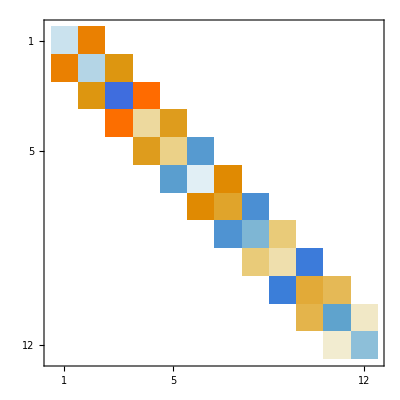

```mathematica
m=12;
S=RandomReal[{-1,1},{m,m}];S=S+Sᵀ;
H = Chop[HessenbergDecomposition[S]⟦2⟧];
MatrixPlot[H]
```